# Muon Production in SM - e^-e^+-> μ^- μ^+

## Load FeynArts and FormCalc

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts-3.11/FeynArts.m"
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
<<"/home/riccardo/Programs/FormCalc/FormCalc-9.10/FormCalc.m"
```

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

```mathematica
Quit[]
```

## Tree-Level

> Top. 1 ad/bdcd/0.m, 0 diagrams

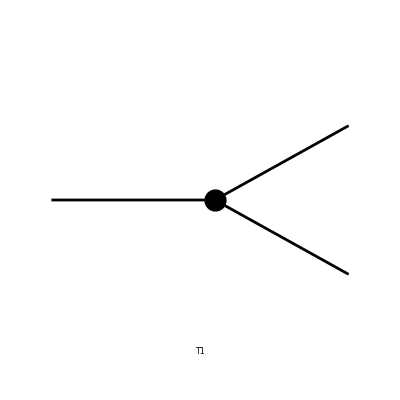

```mathematica
top=CreateTopologies[0,1->2,Adjacencies->3];
Paint[top];
```

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 1 Generic, 1 Classes, 1 Particles insertions

in total: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 1 ad/bdcd/0.m, 0 diagrams

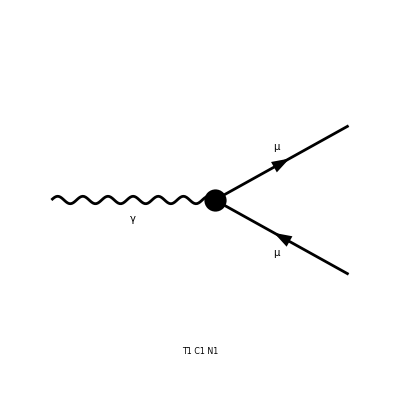

```mathematica
ins=InsertFields[top, {V[1]} -> {F[2,{2}], -F[2,{2}]},InsertionLevel->Particles];
Paint[ins, PaintLevel->{Classes}];
```

```mathematica
amp=CreateFeynAmp[ins,AmplitudeLevel->{Particles}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

FeynAmpList[Process→{{V[1],p1,0,{}}}→{{F[2,{2}],k1,MM,{-Charge,LeptonNumber}},{-F[2,{2}],k2,MM,{Charge,-LeptonNumber}}},Model→{SM},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][FeynAmp[GraphID[Topology==1,Generic==1,Particles==1,Number==1],Integral[],ⅈ ū[k1,MM].(ⅈ EL ga[Lor1].om_-+ⅈ EL ga[Lor1].om_+).v[k2,MM] ep[V[1],p1,Lor1]]]

```mathematica
result=CalcFeynAmp[amp]
```

preparing FORM code in /home/riccardo/fc-amp-4.frm

running FORM...

ok

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-EL (F1+F2)]

## One-Loop

> Top. 1 ad/becf/dedfef.m, 0 diagrams

> Top. 2 ad/bdce/dfefef.m, 0 diagrams

> Top. 3 ad/becd/dfefef.m, 0 diagrams

> Top. 4 ad/bece/efdfdf.m, 0 diagrams

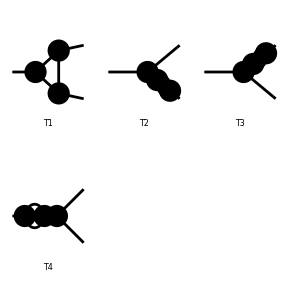

```mathematica
top1=CreateTopologies[1,1->2,Adjacencies->3,ExcludeTopologies->Tadpoles];
Paint[top1];
```

Excluding 2 Generic, 21 Classes, and 25 Particles fields

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 2: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 3: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 4: 1 Generic, 3 Classes, 9 Particles insertions

Restoring 2 Generic, 21 Classes, and 25 Particles fields

in total: 4 Generic, 6 Classes, 12 Particles insertions

> Top. 1 ad/becf/dedfef.m, 0 diagrams

> Top. 2 ad/bdce/dfefef.m, 0 diagrams

> Top. 3 ad/becd/dfefef.m, 0 diagrams

> Top. 4 ad/bece/efdfdf.m, 0 diagrams

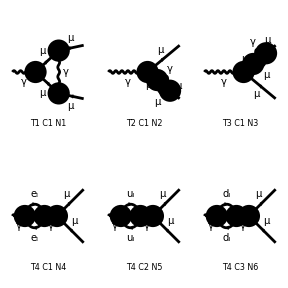

```mathematica
ins1=InsertFields[top1, {V[1]} -> {F[2,{2}], -F[2,{2}]},InsertionLevel->Particles,QEDOnly];
Paint[ins1, PaintLevel->{Classes}];
```

```mathematica
amp1=CreateFeynAmp[ins1,AmplitudeLevel->{Particles}];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

> Top. 3: 1 Particles amplitude

> Top. 4: 9 Particles amplitudes

in total: 12 Particles amplitudes

```mathematica
result1=CalcFeynAmp[amp1]
```

preparing FORM code in /home/riccardo/fc-amp-4.frm

running FORM...

ok

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][1/π Alfa EL (-Sub1 (C0i[cc1,MM2,0,MM2,0,MM2,MM2]+C0i[cc2,MM2,0,MM2,0,MM2,MM2])+(F3+F4) MM Pair1 (C0i[cc11,MM2,0,MM2,0,MM2,MM2]+2 C0i[cc12,MM2,0,MM2,0,MM2,MM2]+C0i[cc22,MM2,0,MM2,0,MM2,MM2])+(F1+F2) (Finite/4-1/2 B0i[bb0,MM2,0,MM2]+C0i[cc00,MM2,0,MM2,0,MM2,MM2]+(A0[ME2]+A0[ML2]+A0[MM2]+1/3 (A0[MB2]+A0[MD2]+A0[MS2])+4/3 (A0[MC2]+A0[MT2]+A0[MU2])-2 (B0i[bb00,0,ME2,ME2]+B0i[bb00,0,ML2,ML2]+B0i[bb00,0,MM2,MM2])-2/3 (B0i[bb00,0,MB2,MB2]+B0i[bb00,0,MD2,MD2]+B0i[bb00,0,MS2,MS2])-8/3 (B0i[bb00,0,MC2,MC2]+B0i[bb00,0,MT2,MT2]+B0i[bb00,0,MU2,MU2])) Den[0,0]+MM2 (-C0i[cc0,MM2,0,MM2,0,MM2,MM2]+(Finite-2 B0i[bb0,MM2,0,MM2]+2 B0i[bb1,MM2,0,MM2]) Den[MM2,MM2])))]

```mathematica
UVDivergentPart[result1]
```

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][1/π Alfa EL (F1+F2) (-Divergence/4+(Divergence ME2+Divergence ML2+Divergence MM2-2 ((Divergence ME2)/2+(Divergence ML2)/2+(Divergence MM2)/2)-2/3 ((Divergence MB2)/2+(Divergence MD2)/2+(Divergence MS2)/2)+1/3 (Divergence MB2+Divergence MD2+Divergence MS2)-8/3 ((Divergence MC2)/2+(Divergence MT2)/2+(Divergence MU2)/2)+4/3 (Divergence MC2+Divergence MT2+Divergence MU2)) Den[0,0]-3 Divergence MM2 Den[MM2,MM2])]

> Top. 1 ad/becf/dedfef.m, 0 diagrams

> Top. 2 ad/bdce/dfefef.m, 0 diagrams

> Top. 3 ad/becd/dfefef.m, 0 diagrams

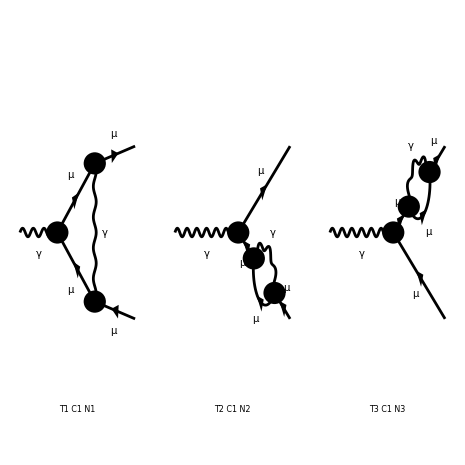

```mathematica
insPart1=Delete[ins1,4];
Paint[insPart1, PaintLevel->{Classes}];
```